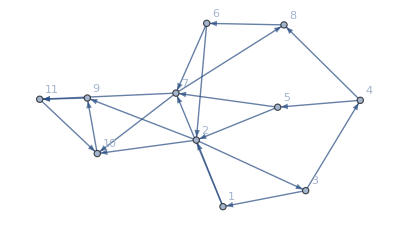

```mathematica
Graph[{3->1,
2->3,
3->4,
4->5,
4->8,
8->6,
7->8,
1->2,
1->7,
5->2,
5->7,
6->2,
6->7,

2->9,
2->10,
7->10,
7->11,
11->10,
10->9,
9->11
},VertexLabels->"Name"]
```

```mathematica
g0=-Graphics-;
```

```mathematica
EdgeList[g0]
```

```mathematica
h1[n_]:=Block[{blist=PadLeft[IntegerDigits[n,2],20],uelist={{3,1},{2,3},{3,4},{4,5},{4,8},{8,6},{7,8},{1,2},{1,7},{5,2},{5,7},{6,2},{6,7},{2,9},{2,10},{7,10},{7,11},{11,10},{10,9},{9,11}}},
Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,20}]],∞,All]]]
```

```mathematica
Monitor[First[Last[Reap[Do[If[h1[j]≥45,Sow[j]],{j,0,2^20}]]]],{j,i}]
```

{445086,510622,537953,603489}

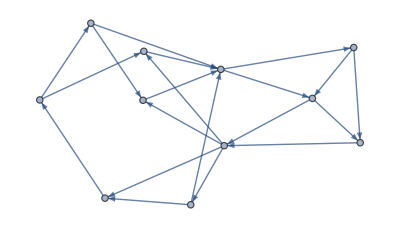
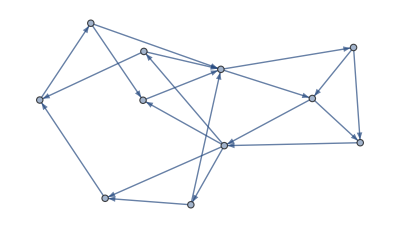
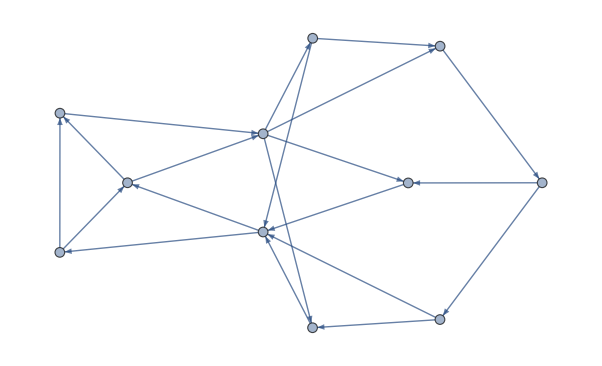
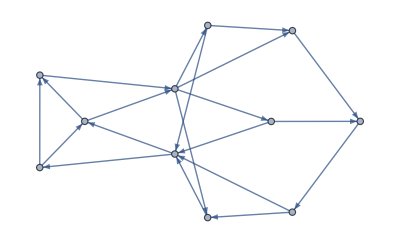

```mathematica
Map[Block[{blist=PadLeft[IntegerDigits[#,2],20],uelist={{3,1},{2,3},{3,4},{4,5},{4,8},{8,6},{7,8},{1,2},{1,7},{5,2},{5,7},{6,2},{6,7},{2,9},{2,10},{7,10},{7,11},{11,10},{10,9},{9,11}}},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,20}]]]&,{445086,510622,537953,603489}]
```

```mathematica
{189432,190456,858119,859143}
```

```mathematica
Map[{#[[1]],#[[2]]}&,{3<->1,2<->3,3<->4,4<->5,4<->8,8<->6,7<->8,1<->2,1<->7,5<->2,5<->7,6<->2,6<->7,2<->9,2<->10,7<->10,7<->11,11<->10,10<->9,9<->11}]
```

{{3,1},{2,3},{3,4},{4,5},{4,8},{8,6},{7,8},{1,2},{1,7},{5,2},{5,7},{6,2},{6,7},{2,9},{2,10},{7,10},{7,11},{11,10},{10,9},{9,11}}

```mathematica
StringReplace["{3->1,2->3,3->4,4->5,4->8,8->6,7->8,1->2,1->7,5->2,5->7,6->2,6->7,2->9,2->10,7->10,7->11,11->10,10->9,9->11}",{"->"->"<->"}]
```

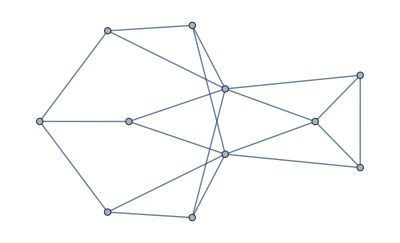

```mathematica
Graph[{3<->1,2<->3,3<->4,4<->5,4<->8,8<->6,7<->8,1<->2,1<->7,5<->2,5<->7,6<->2,6<->7,2<->9,2<->10,7<->10,7<->11,11<->10,10<->9,9<->11}]
```

```mathematica
PlanarGraphQ[g0]
```

False

```mathematica
Length[FindCycle[g0,∞,All]]
```

7

```mathematica
MatrixForm[AdjacencyMatrix[UndirectedGraph[g0]]]
```

```mathematica
f0[{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_,t_}]:=Normal[{{0,a,b,c,0,0,0,0,0,0,0},{1-a,0,d,0,0,0,0,e,0,0,0},{1-b,1-d,0,0,f,0,g,0,h,i,0},{1-c,0,0,0,j,k,0,0,0,0,0},{0,0,1-f,1-j,0,0,0,l,0,0,0},{0,0,0,1-k,0,0,m,n,0,0,0},{0,0,1-g,0,0,1-m,0,o,0,0,0},{0,1-e,0,0,1-l,1-n,1-o,0,0,p,q},{0,0,1-h,0,0,0,0,0,0,r,s},{0,0,1-i,0,0,0,0,1-p,1-r,0,t},{0,0,0,0,0,0,0,1-q,1-s,1-t,0}}]
fl[n_]:=Length[FindCycle[AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],20]]],∞,All]]
fl[2]
```

1

```mathematica
f0[PadLeft[IntegerDigits[1,2],20]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

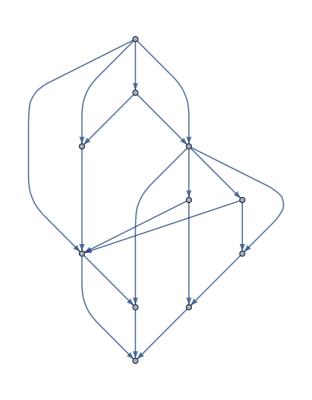

```mathematica
AdjacencyGraph[f0[PadLeft[IntegerDigits[1,2],20]]]
```

```mathematica
thlist=Timing[Monitor[Table[fl[i],{i,1,2^20}],i]]
```

{589.40454,{0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,1,1,2,1,1,2,1,1,2,1,3,1,3,3,2,1,1,2,3,3,1,3,1,2,1,1,2,1,1,2,1,1,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,1048268,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,1,1,2,1,1,2,1,1,2,1,3,1,3,3,2,1,1,2,3,3,1,3,1,2,1,1,2,1,1,2,1,1,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,2,0,2,2,1,0,0,1,2,2,0,2,0,1,0,0,1,0,0,1,0,0,0}}
 |  |  |  |

```mathematica
Max[Last[Out[77]]]
```

45

```mathematica
Flatten[Position[Last[Out[77]],45]]
```

```mathematica
Map[AdjacencyGraph[f0[PadLeft[IntegerDigits[#,2],20]]]&,{189432,190456,858119,859143}]
```

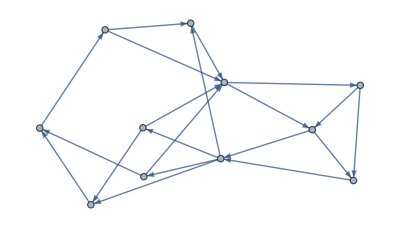
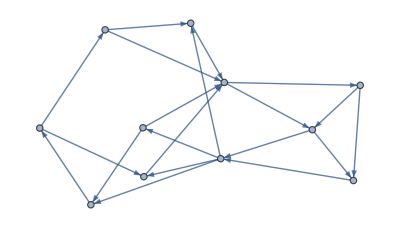
```mathematica
Map[GraphPlot[#,Method->"SpringEmbedding"]&,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

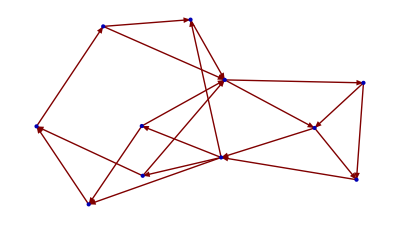
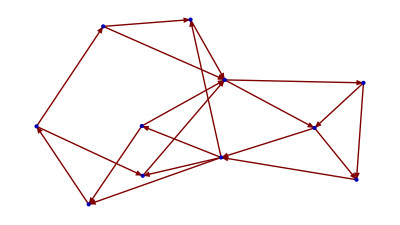
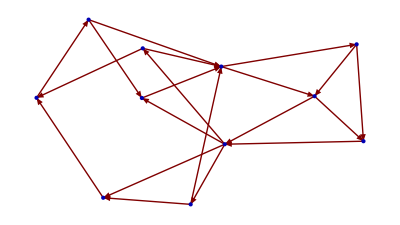
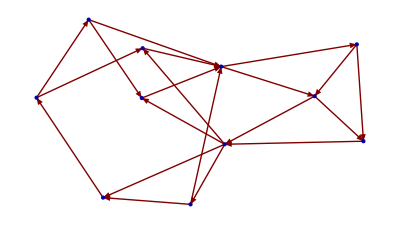

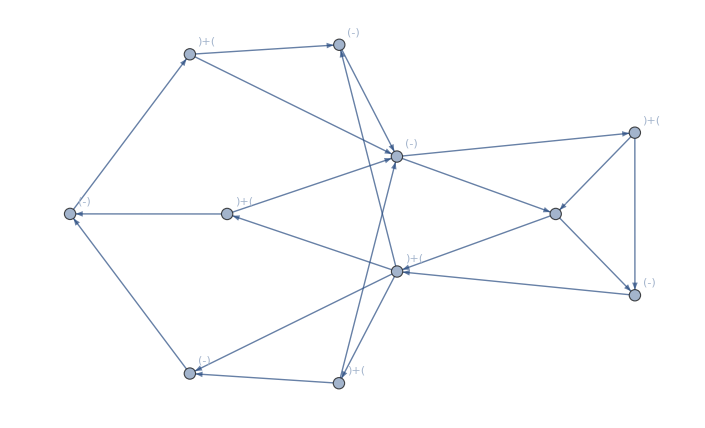
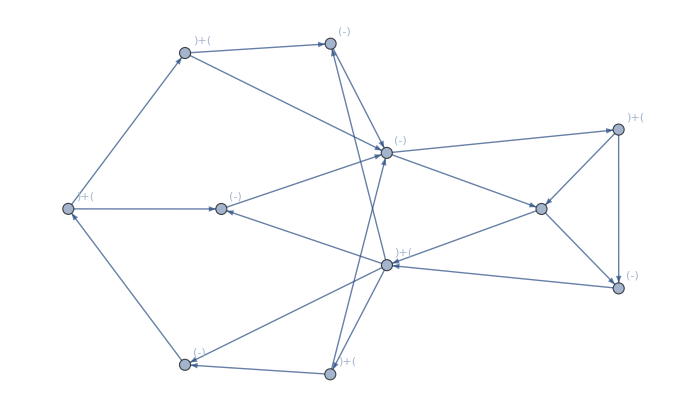
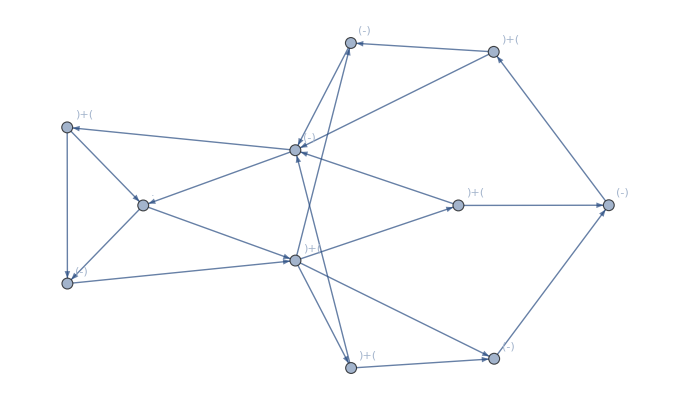
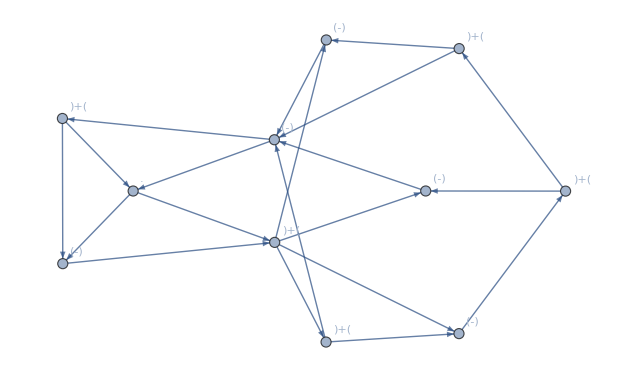

```mathematica
Map[signedplot,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
GraphAutomorphismGroup[UndirectedGraph[-Graphics-]]
```

```mathematica
GroupOrder[PermutationGroup[{Cycles[{{1,8},{3,7},{4,5},{10,11}}]}]]
```

2

```mathematica
EdgeList[-Graphics-]
```

{1->4,2->1,2->8,3->1,3->2,3->5,3->7,4->6,5->4,5->8,6->7,6->8,7->8,8->10,8->11,9->3,10->3,10->9,11->9,11->10}

```mathematica
check3[graph_]:=Block[{mat=AdjacencyMatrix[graph]},Or@@Map[mat[[#[[1]],#[[2]]]]+mat[[#[[2]],#[[3]]]]==2&,Tuples[VertexList[graph],3]]]
```

```mathematica
check4[graph_]:=(¬MemberQ[Join[VertexInDegree[graph],VertexOutDegree[graph]],0])∧check3[graph]
```

```mathematica
check4[-Graphics-]
```

True

```mathematica
check3[-Graphics-]
```

True

```mathematica
f3[n_]:=check4[AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],20]]]]
```

```mathematica
thlist2=Timing[Monitor[Table[f3[i],{i,1,2^20}],i]]
```

{1145.59838,{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,1048474,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}}
 |  |  |  |

```mathematica
Flatten[Position[Last[%109],True]]
```

{131650,131653,131656,131658,131660,131661,131665,131666,131667,131669,131672,131673,131674,131676,131677,131714,131717,131720,131722,131724,131725,131729,131730,131731,131733,131746,131749,131752,131754,131756,131757,131761,131762,131763,131765,131768,131769,131770,131772,131773,131778,131781,131784,131786,131788,131789,131793,131794,131795,88914,916780,916781,916782,916786,916787,916789,916791,916794,916797,916802,916803,916805,916806,916807,916810,916812,916813,916814,916818,916819,916821,916823,916826,916829,916842,916844,916845,916846,916850,916851,916853,916855,916858,916861,916898,916899,916901,916902,916903,916906,916908,916909,916910,916914,916915,916917,916919,916922,916925}
 |  |  |  |

```mathematica
f4[n_]:=Boole[(Det[AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],20]]]]≠0)]
```

```mathematica
thlist4=Timing[Monitor[Table[f4[i],{i,1,2^20}],i]]
```

$Aborted[]

```mathematica
Flatten[Position[Last[Out[115]],1]]
```

```mathematica
Map[Det[AdjacencyMatrix[#]]&,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,0,0,0}

```mathematica
Det[AdjacencyMatrix[-Graphics-]]
```

0

```mathematica
Table[MatrixPower[AdjacencyMatrix[g0],i]//MatrixForm,{i,2,10}]
```

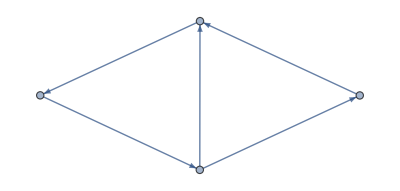

```mathematica
g1=Graph[{1->2,
2->4,
4->3,
3->1,
1->4}]
```

```mathematica
g12=Graph[{1->2,
2->4,
4->3,
3->1,
4->1}]
```

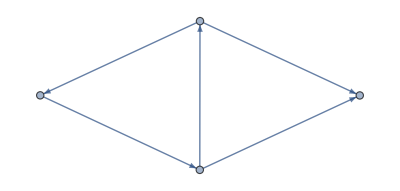

```mathematica
g10=Graph[{1->2,
4->2,
4->3,
3->1,
1->4}]
```

```mathematica
{MatrixForm[AdjacencyMatrix[g1]],MatrixForm[Inverse[AdjacencyMatrix[g1]]]}
```

{(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | -1 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)}

```mathematica
Inverse[({{0, 1, 1, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}}),Modulus->2]//MatrixForm
```

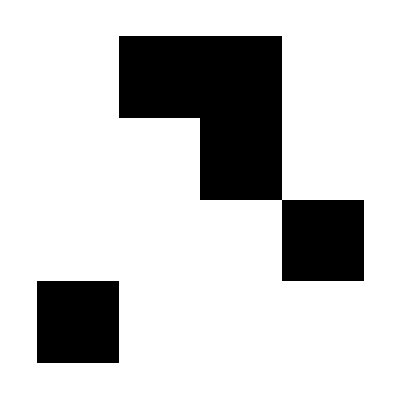
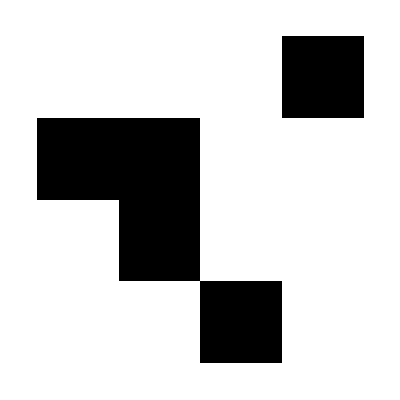

```mathematica
{ArrayPlot[({{0, 1, 1, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}})],ArrayPlot[({{0, 0, 0, 1}, {1, 1, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}})]}
```

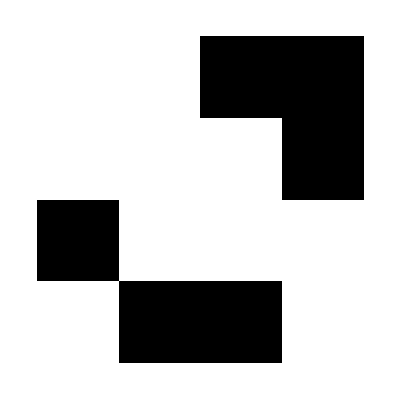
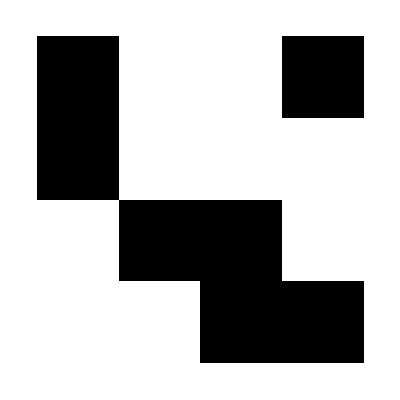
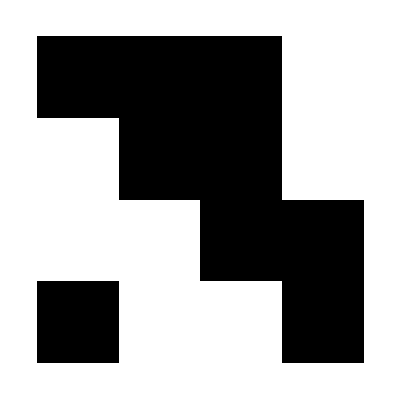
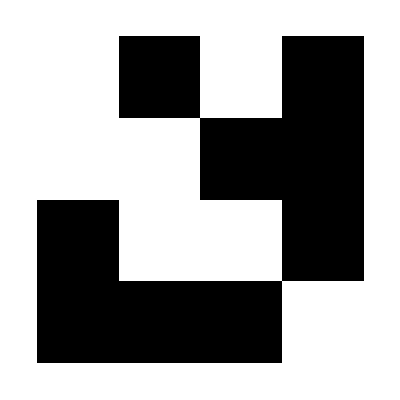
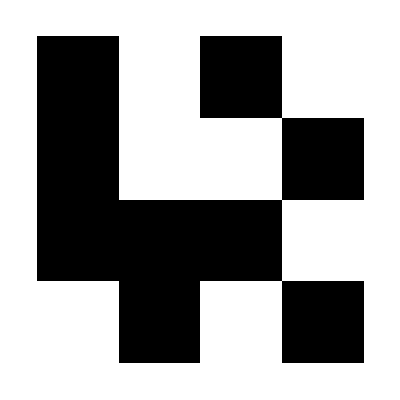
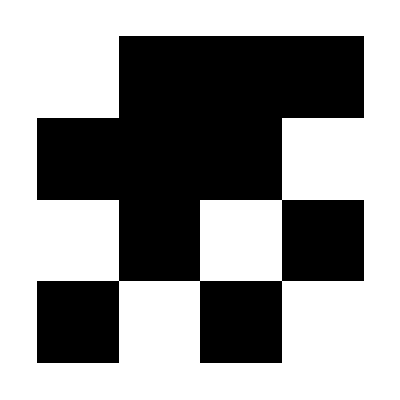
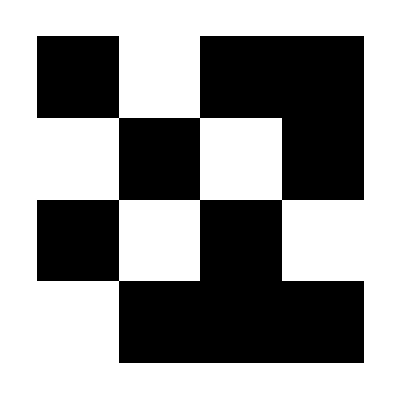
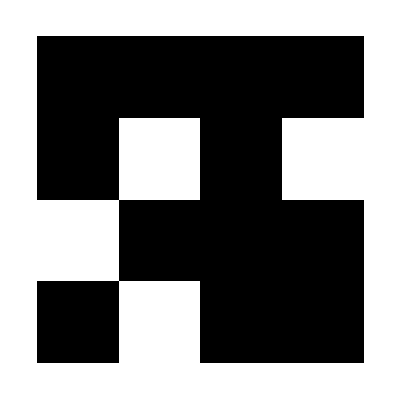
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[Mod[MatrixPower[({{0, 1, 1, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}}),i],2]],{i,1,15}]
```

```mathematica
numcy[graph_]:=Length[FindCycle[graph,∞,All]]
```

```mathematica
Map[numcy,Table[AdjacencyGraph[Mod[MatrixPower[({{0, 1, 1, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}}),i],2]],{i,1,15}]]
```

{2,3,1,2,10,3,8,3,8,10,7,7,3,1,0}

```mathematica
Map[numcy,Table[AdjacencyGraph[Mod[MatrixPower[AdjacencyMatrix[g12],i],2]],{i,1,15}]]
```

{2,3,1,2,10,3,8,3,8,10,7,7,3,1,0}

```mathematica
Map[numcy,Table[AdjacencyGraph[Mod[MatrixPower[AdjacencyMatrix[g10],i],2]],{i,1,15}]]
```

{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0}

```mathematica
Det[AdjacencyMatrix[g10]]
```

0

```mathematica
Det[Transpose[AdjacencyMatrix[g10]]]
```

0

```mathematica
Det[Transpose[AdjacencyMatrix[g1]]]
```

-1

```mathematica
oq[mat_]:=(Transpose[mat].mat==IdentityMatrix[Length[mat]])
```

```mathematica
iq[mat_]:=(Mod[Det[mat],2]≠0)
```

```mathematica
iq[AdjacencyMatrix[g1]]
```

True

```mathematica
tt[mat_]:=Block[{iqq=iq[mat]},Piecewise[{{Block[{sq=SimpleGraphQ[AdjacencyGraph[mat]]},Piecewise[{{Block[{cq=ConnectedGraphQ[AdjacencyGraph[mat]]},Piecewise[{{Block[{qq=MemberQ[VertexDegree[UndirectedGraph[AdjacencyGraph[mat]]],1]},Piecewise[{{True, ¬qq}, {False, qq}}]], cq}, {False, ¬cq}}]], sq}, {False, ¬sq}}]], iqq}, {False, ¬iqq}}]]
```

```mathematica
Reap[ParallelDo[If[tt[Partition[PadLeft[IntegerDigits[n,2],25],5]],Sow[n]],{n,1,2^25}]]
```

$Aborted

```mathematica
Monitor[Table[Boole[iq[Partition[PadLeft[IntegerDigits[n,2],25],5]]],{n,0,2^25}],n]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,65193,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Flatten[Position[%,1]]
```

{4681,4682,4683,4684,4685,4686,4687,4688,4697,4698,4699,4700,4701,4702,4703,4704,4713,4714,4715,4716,4717,4718,4719,4720,4729,4730,4731,4732,4733,4734,4735,4736,4741,4742,4743,4744,4749,4750,4751,4752,4757,4758,4759,4760,4765,4766,4767,4768,4773,4774,4775,4776,4781,4782,4783,4784,4789,4790,4791,4792,4797,4798,20036,65125,65126,65131,65132,65133,65134,65139,65140,65141,65142,65147,65148,65149,65150,65155,65156,65157,65158,65163,65164,65165,65166,65171,65172,65173,65174,65179,65180,65181,65182,65187,65188,65191,65192,65193,65194,65197,65198,65203,65204,65207,65208,65209,65210,65213,65214,65221,65222,65223,65224,65225,65226,65227,65228,65237,65238,65239,65240,65241,65242,65243,65244}
 |  |  |  |

```mathematica
sncq[graph_]:=ConnectedGraphQ[graph]∧SimpleGraphQ[graph]∧(¬MemberQ[VertexDegree[UndirectedGraph[graph]],0])∧(¬MemberQ[VertexDegree[UndirectedGraph[graph]],1])
```

```mathematica
Monitor[Table[Boole[sncq[AdjacencyGraph[Partition[PadLeft[IntegerDigits[Out[11][[j]],2],16],4]]]],{j,1,Length[Out[11]]}],j]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,19815,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Flatten[Position[%,1]]
```

```mathematica
{34,38,42,46,66,72,74,80,130,134,138,142,162,166,168,170,174,176,790,792,794,798,800,818,822,826,830,834,836,838,842,844,846,886,888,890,894,896,914,918,922,926,930,932,934,938,940,942,1346,1348,1350,1354,1356,1358,1412,1414,1416,1420,1422,1424,1442,1444,1446,1450,1452,1454,1486,1508,1510,1512,1516,1518,1520,1922,1926,1946,1949,1950,1970,1974,1994,1997,1998,2018,2022,2033,2035,2036,2041,2042,2047,2081,2087,2089,2090,2091,2092,2114,2118,2138,2141,2142,2162,2166,2186,2189,2190,2210,2214,2225,2227,2228,2233,2234,2239,2273,2279,2281,2282,2283,2284,2690,2692,2694,2698,2700,2702,2754,2756,2758,2760,2762,2764,2766,2768,2796,2798,2818,2822,2826,2830,2850,2856,2858,2864,3266,3270,3281,3283,3285,3287,3289,3292,3293,3314,3318,3329,3331,3333,3335,3337,3340,3341,3362,3366,3377,3379,3382,3385,3388,3390,3391,3410,3414,3425,3428,3430,3431,3433,3435,3438,3458,3462,3473,3475,3478,3481,3484,3486,3487,3506,3510,3521,3526,3527,3529,3531,3534,3554,3558,3569,3571,3573,3575,3577,3580,3581,3602,3606,3617,3619,3621,3623,3625,3628,3629,4130,4132,4134,4146,4148,4150,4170,4171,4172,4202,4203,4204,4226,4228,4230,4242,4244,4246,4257,4259,4261,4263,4265,4267,4270,4289,4291,4293,4295,4297,4299,4302,4804,4806,4808,4828,4830,4832,4859,4862,4883,4886,4900,4902,4904,4924,4926,4928,4945,4947,4949,4951,4953,4954,4955,4956,4969,4971,4973,4975,4977,4978,4979,4980,5474,5476,5478,5505,5506,5509,5510,5513,5514,5519,5537,5538,5543,5545,5546,5549,5550,5570,5572,5574,5586,5590,5601,5604,5605,5609,5612,5614,5615,5633,5636,5638,5639,5641,5644,5645,6146,6148,6150,6152,6174,6176,6193,6194,6197,6198,6201,6204,6206,6207,6217,6222,6223,6225,6226,6229,6230,6242,6244,6246,6248,6270,6272,6289,6292,6293,6297,6298,6303,6313,6314,6319,6321,6324,6325,6738,6740,6742,6746,6748,6750,6756,6760,6764,6766,6768,6788,6790,6796,6798,6818,6820,6822,6834,6836,6838,6858,6859,6860,6890,6891,6892,6914,6916,6918,6930,6932,6934,6945,6948,6949,6953,6956,6958,6959,6977,6980,6982,6983,6985,6988,6989,7298,7300,7302,7304,7332,7333,7346,7348,7350,7352,7380,7381,7394,7396,7398,7400,7417,7419,7420,7425,7428,7430,7431,7444,7448,7465,7468,7470,7471,7473,7474,7475,7476,7490,7492,7494,7524,7526,7527,7548,7550,7551,7562,7564,7566,7586,7588,7590,7609,7611,7612,7617,7620,7621,7633,7636,7637,7641,7642,7643,7644,7660,7662,8082,8084,8086,8090,8092,8094,8100,8104,8108,8110,8112,8132,8134,8140,8142,8162,8164,8166,8193,8194,8197,8198,8201,8202,8207,8225,8226,8231,8233,8234,8237,8238,8258,8260,8262,8274,8276,8278,8289,8291,8293,8295,8297,8299,8302,8321,8323,8325,8327,8329,8331,8334,8642,8644,8646,8648,8665,8667,8669,8671,8673,8674,8677,8678,8690,8692,8694,8696,8713,8715,8717,8719,8721,8722,8725,8726,8738,8740,8742,8744,8761,8763,8766,8769,8770,8775,8788,8792,8809,8810,8815,8817,8819,8822,8834,8836,8838,8857,8859,8862,8865,8866,8869,8870,8881,8882,8885,8886,8889,8891,8894,8906,8908,8910,8930,8932,8934,8953,8955,8957,8959,8961,8962,8967,8977,8979,8981,8983,8985,8986,8991,9002,9004,9006}
```

{34,38,42,46,66,72,74,80,130,134,138,142,162,166,168,170,174,176,790,792,794,798,800,818,822,826,830,834,836,838,842,844,846,886,888,890,894,896,914,918,922,926,930,932,934,938,940,942,1346,1348,1350,1354,1356,1358,1412,1414,1416,1420,1422,1424,1442,1444,1446,1450,1452,1454,1486,1508,1510,1512,1516,1518,1520,1922,1926,1946,1949,1950,1970,1974,1994,1997,1998,2018,2022,2033,2035,2036,2041,2042,2047,2081,2087,2089,2090,2091,2092,2114,2118,2138,2141,2142,2162,2166,2186,2189,2190,2210,2214,2225,2227,2228,2233,2234,2239,2273,2279,2281,2282,2283,2284,2690,2692,2694,2698,2700,2702,2754,2756,2758,2760,2762,2764,2766,2768,2796,2798,2818,2822,2826,2830,2850,2856,2858,2864,3266,3270,3281,3283,3285,3287,3289,3292,3293,3314,3318,3329,3331,3333,3335,3337,3340,3341,3362,3366,3377,3379,3382,3385,3388,3390,3391,3410,3414,3425,3428,3430,3431,3433,3435,3438,3458,3462,3473,3475,3478,3481,3484,3486,3487,3506,3510,3521,3526,3527,3529,3531,3534,3554,3558,3569,3571,3573,3575,3577,3580,3581,3602,3606,3617,3619,3621,3623,3625,3628,3629,4130,4132,4134,4146,4148,4150,4170,4171,4172,4202,4203,4204,4226,4228,4230,4242,4244,4246,4257,4259,4261,4263,4265,4267,4270,4289,4291,4293,4295,4297,4299,4302,4804,4806,4808,4828,4830,4832,4859,4862,4883,4886,4900,4902,4904,4924,4926,4928,4945,4947,4949,4951,4953,4954,4955,4956,4969,4971,4973,4975,4977,4978,4979,4980,5474,5476,5478,5505,5506,5509,5510,5513,5514,5519,5537,5538,5543,5545,5546,5549,5550,5570,5572,5574,5586,5590,5601,5604,5605,5609,5612,5614,5615,5633,5636,5638,5639,5641,5644,5645,6146,6148,6150,6152,6174,6176,6193,6194,6197,6198,6201,6204,6206,6207,6217,6222,6223,6225,6226,6229,6230,6242,6244,6246,6248,6270,6272,6289,6292,6293,6297,6298,6303,6313,6314,6319,6321,6324,6325,6738,6740,6742,6746,6748,6750,6756,6760,6764,6766,6768,6788,6790,6796,6798,6818,6820,6822,6834,6836,6838,6858,6859,6860,6890,6891,6892,6914,6916,6918,6930,6932,6934,6945,6948,6949,6953,6956,6958,6959,6977,6980,6982,6983,6985,6988,6989,7298,7300,7302,7304,7332,7333,7346,7348,7350,7352,7380,7381,7394,7396,7398,7400,7417,7419,7420,7425,7428,7430,7431,7444,7448,7465,7468,7470,7471,7473,7474,7475,7476,7490,7492,7494,7524,7526,7527,7548,7550,7551,7562,7564,7566,7586,7588,7590,7609,7611,7612,7617,7620,7621,7633,7636,7637,7641,7642,7643,7644,7660,7662,8082,8084,8086,8090,8092,8094,8100,8104,8108,8110,8112,8132,8134,8140,8142,8162,8164,8166,8193,8194,8197,8198,8201,8202,8207,8225,8226,8231,8233,8234,8237,8238,8258,8260,8262,8274,8276,8278,8289,8291,8293,8295,8297,8299,8302,8321,8323,8325,8327,8329,8331,8334,8642,8644,8646,8648,8665,8667,8669,8671,8673,8674,8677,8678,8690,8692,8694,8696,8713,8715,8717,8719,8721,8722,8725,8726,8738,8740,8742,8744,8761,8763,8766,8769,8770,8775,8788,8792,8809,8810,8815,8817,8819,8822,8834,8836,8838,8857,8859,8862,8865,8866,8869,8870,8881,8882,8885,8886,8889,8891,8894,8906,8908,8910,8930,8932,8934,8953,8955,8957,8959,8961,8962,8967,8977,8979,8981,8983,8985,8986,8991,9002,9004,9006}

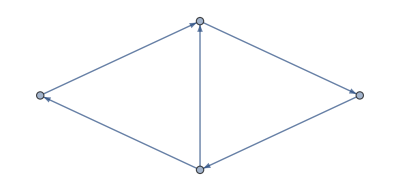
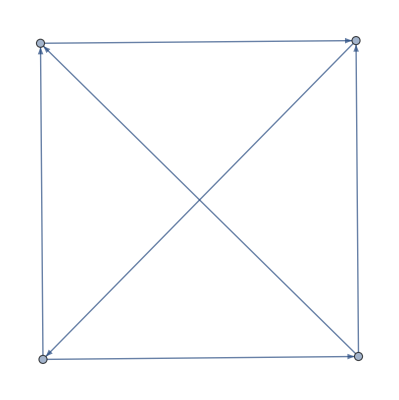
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[Select[Map[AdjacencyGraph[Partition[PadLeft[IntegerDigits[#,2],16],4]]&,%],SimpleGraphQ],ConnectedGraphQ]
```